```mathematica
Manipulate[Module[{h}, h=0.2286;Plot[Sqrt[(d-h*Sin[t Degree])^2 + (h*Cos[t Degree])^2]/d,{t,-90,90},AxesLabel->{"Angle (deg)","Effective head-mic distance (relative)"},PlotRange->{0.5,1.5}]],{{d,1,"Tripod distance"},0.5,10,0.25,Appearance->"Labeled"}]
```

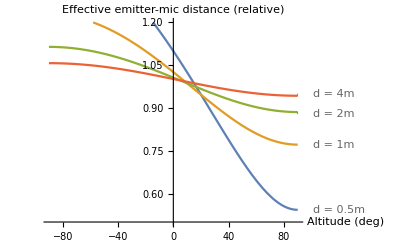

```mathematica
Module[{h}, h=0.2286;dist={0.5,1,2,4};Plot[Table[Sqrt[(d-h*Sin[t Degree])^2 + (h*Cos[t Degree])^2]/d,{d,dist}]//Evaluate,{t,-90,90},AxesLabel->{"Altitude (deg)","Effective emitter-mic distance (relative)"},PlotRange->{0.5,1.2},PlotLabels->(("d = "<>ToString[#]<>"m")&/@ dist)]]
```

```mathematica
Table[θ->Round[{d,39.37 * d},0.01]/.Module[{D=1,h=0.2032},Solve[(h*Cos[θ Degree])^2 + (d-h*Sin[θ Degree])^2 == D^2 &&d>0,d]],{θ,-50,90,10}]
```

{{-50→{0.84,32.9}},{-40→{0.86,33.75}},{-30→{0.88,34.76}},{-20→{0.91,35.91}},{-10→{0.94,37.18}},{0→{0.98,38.55}},{10→{1.02,39.96}},{20→{1.05,41.38}},{30→{1.09,42.76}},{40→{1.12,44.03}},{50→{1.15,45.16}},{60→{1.17,46.09}},{70→{1.19,46.79}},{80→{1.2,47.22}},{90→{1.2,47.37}}}